# Linear Theory of Ion-acoustic Instability

```mathematica
ZPrincipal[ζ_]:=- Sqrt[π] ⅇ^(-ζ^2) Erfi[ζ];
ZDelta[ζ_]:= Sqrt[π] ⅇ^(-ζ^2);
```

## Temperature-ratio=50, mass-ratio=25

```mathematica
ϵT=1/50; (*Temperature ratio*)
ϵM =1/25; (*Mass ratio*)
ωpe=1;
vTe = 0.02;
ωpi:=Sqrt[ϵM]*ωpe;
cs := vTe * Sqrt[ϵM];
λe:=vTe / ωpe;
λi:=Sqrt[ϵT]*λe;
vTi:=λi *ωpi;
ke := (2 π)/λe;
u:=0.02
ζe:=(ω-k *u)/(k *Sqrt[2]*vTe); ζi:=ω/(k*Sqrt[2]*vTi);
t[k_?NumericQ]:=FindRoot[(1+(1 + (ω-k *u)/(k *Sqrt[2]*vTe) ZPrincipal[(ω-k *u)/(k *Sqrt[2]*vTe)])/(k^2 λe^2)+(1 + ω/(k*Sqrt[2]*vTi) ZPrincipal[ω/(k*Sqrt[2]*vTi)])/(k^2 λi^2) +ⅈ (((ω-k *u)/(k *Sqrt[2]*vTe) ZDelta[(ω-k *u)/(k *Sqrt[2]*vTe)])/(k^2 λe^2)+(ω/(k*Sqrt[2]*vTi) ZDelta[ω/(k*Sqrt[2]*vTi)])/(k^2 λi^2)) ),{ω, 0.04}]
p[k_] :=Im[ω/.t[k]]
w[k_] :=Re[ω/.t[k]]
```

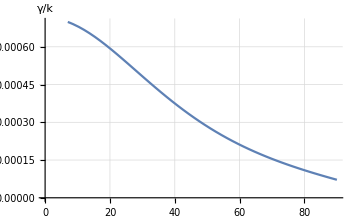

```mathematica
Plot[p[k]/k,{k,7,90},AxesOrigin->{0,0},GridLines->Automatic, AxesLabel->γ/k]
```

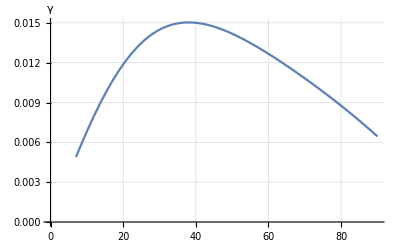

```mathematica
Plot[p[k],{k,7,90},AxesOrigin->{0,0},GridLines->Automatic, AxesLabel->γ]
```

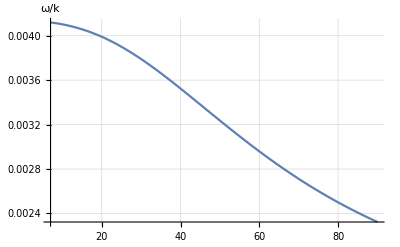

```mathematica
Plot[w[k]/k,{k,7,90} ,GridLines->Automatic,AxesLabel->ω/k]
```

## Temperature-ratio=50, mass-ratio=400

```mathematica
ϵT=1/50; (*Temperature ratio*)
ϵM =1/400; (*Mass ratio*)
ωpe=1;
vTe = 0.02;
ωpi:=Sqrt[ϵM]*ωpe;
cs := vTe * Sqrt[ϵM];
λe:=vTe / ωpe;
λi:=Sqrt[ϵT]*λe;
vTi:=λi *ωpi;
ke := (2 π)/λe;
u:=0.01
ζe:=(ω-k *u)/(k *Sqrt[2]*vTe); ζi:=ω/(k*Sqrt[2]*vTi);
t[k_?NumericQ]:=FindRoot[(1+(1 + (ω-k *u)/(k *Sqrt[2]*vTe) ZPrincipal[(ω-k *u)/(k *Sqrt[2]*vTe)])/(k^2 λe^2)+(1 + ω/(k*Sqrt[2]*vTi) ZPrincipal[ω/(k*Sqrt[2]*vTi)])/(k^2 λi^2) +ⅈ (((ω-k *u)/(k *Sqrt[2]*vTe) ZDelta[(ω-k *u)/(k *Sqrt[2]*vTe)])/(k^2 λe^2)+(ω/(k*Sqrt[2]*vTi) ZDelta[ω/(k*Sqrt[2]*vTi)])/(k^2 λi^2)) ),{ω, 0.010}]
p[k_] :=Im[ω/.t[k]]
w[k_] :=Re[ω/.t[k]]
```

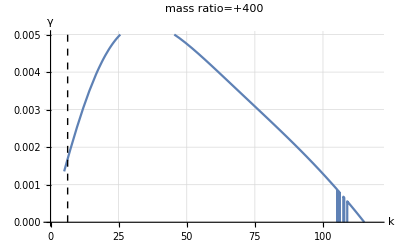

```mathematica
linestyle = {Dashed};
line = Line[{{6.28,0.0},{6.28,0.03}}];
Plot[p[k],{k,5,120},AxesOrigin->{0,0},GridLines->Automatic, AxesLabel->{k,γ}, Epilog->{Directive[linestyle],line}, PlotRange->{0.000,0.005}, PlotLabel->"mass ratio=" +1/ϵM,BaseStyle->{FontSize-> 20}]
```

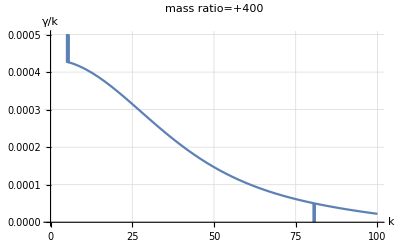

```mathematica
Plot[p[k]/k,{k,5,100},GridLines->Automatic,AxesLabel->{k,γ/k},PlotLabel->"mass ratio=" +1/ϵM,BaseStyle->{FontSize-> 20}, PlotRange->{0.000,0.0005}]
```

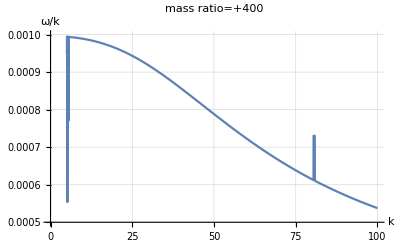

```mathematica
Plot[w[k]/k,{k,5,100},GridLines->Automatic,AxesLabel->{k,ω/k},PlotLabel->"mass ratio=" +1/ϵM,BaseStyle->{FontSize-> 20}, PlotRange->{0.0005,0.0010}]
```

## Temperature-ratio=2, mass-ratio=400

```mathematica
ϵT=1/2; (*Temperature ratio*)
ϵM =1/400; (*Mass ratio*)
ωpe=1;
vTe = 0.02;
ωpi:=Sqrt[ϵM]*ωpe;
cs := vTe * Sqrt[ϵM];
λe:=vTe / ωpe;
λi:=Sqrt[ϵT]*λe;
vTi:=λi *ωpi;
ke := (2 π)/λe;
u:=0.0339
ζe:=(ω-k *u)/(k *Sqrt[2]*vTe); ζi:=ω/(k*Sqrt[2]*vTi);
t[k_?NumericQ]:=FindRoot[(1+(1 + (ω-k *u)/(k *Sqrt[2]*vTe) ZPrincipal[(ω-k *u)/(k *Sqrt[2]*vTe)])/(k^2 λe^2)+(1 + ω/(k*Sqrt[2]*vTi) ZPrincipal[ω/(k*Sqrt[2]*vTi)])/(k^2 λi^2) +ⅈ (((ω-k *u)/(k *Sqrt[2]*vTe) ZDelta[(ω-k *u)/(k *Sqrt[2]*vTe)])/(k^2 λe^2)+(ω/(k*Sqrt[2]*vTi) ZDelta[ω/(k*Sqrt[2]*vTi)])/(k^2 λi^2)) ),{ω, 0.01}]
p[k_] :=Im[ω/.t[k]]
w[k_] :=Re[ω/.t[k]]
```

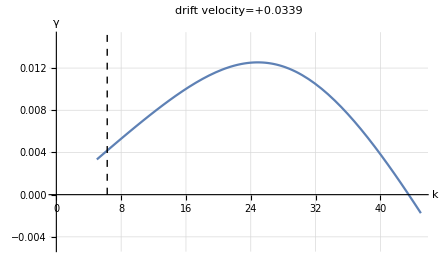

```mathematica
linestyle = {Dashed};
line = Line[{{6.28,0.0},{6.28,0.03}}];
Plot[p[k],{k,5,45},AxesOrigin->{0,0},GridLines->Automatic, AxesLabel->{k,γ}, Epilog->{Directive[linestyle],line}, PlotRange->{-0.005,0.015}, PlotLabel->"drift velocity=" +u,BaseStyle->{FontSize-> 20}]
```

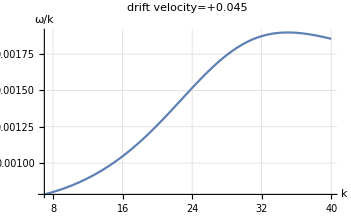

```mathematica
Plot[w[k]/k,{k,7,40},GridLines->Automatic,AxesLabel->{k,ω/k},PlotLabel->"drift velocity=" +u,BaseStyle->{FontSize-> 20}]
```

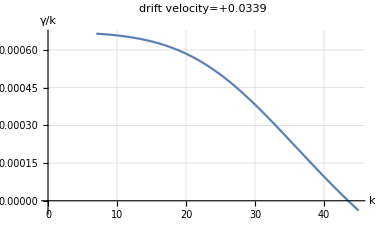

```mathematica
Plot[p[k]/k,{k,7,45},AxesOrigin->{0,0},GridLines->Automatic, AxesLabel->{k,γ/k},PlotLabel->"drift velocity=" +u,BaseStyle->{FontSize-> 20}]
```

## Temperature - ratio = 50, mass - ratio = 100

```mathematica
ϵT=1/50; (*Temperature ratio*)
ϵM =1/100; (*Mass ratio*)
ωpe=1;
vTe = 0.02;
ωpi:=Sqrt[ϵM]*ωpe;
cs := vTe * Sqrt[ϵM];
λe:=vTe / ωpe;
λi:=Sqrt[ϵT]*λe;
vTi:=λi *ωpi;
ke := (2 π)/λe;
u:=0.01
ζe:=(ω-k *u)/(k *Sqrt[2]*vTe); ζi:=ω/(k*Sqrt[2]*vTi);
t[k_?NumericQ]:=FindRoot[(1+(1 + (ω-k *u)/(k *Sqrt[2]*vTe) ZPrincipal[(ω-k *u)/(k *Sqrt[2]*vTe)])/(k^2 λe^2)+(1 + ω/(k*Sqrt[2]*vTi) ZPrincipal[ω/(k*Sqrt[2]*vTi)])/(k^2 λi^2) +ⅈ (((ω-k *u)/(k *Sqrt[2]*vTe) ZDelta[(ω-k *u)/(k *Sqrt[2]*vTe)])/(k^2 λe^2)+(ω/(k*Sqrt[2]*vTi) ZDelta[ω/(k*Sqrt[2]*vTi)])/(k^2 λi^2)) ),{ω, 0.001}]
p[k_] :=Im[ω/.t[k]]
w[k_] :=Re[ω/.t[k]]
```

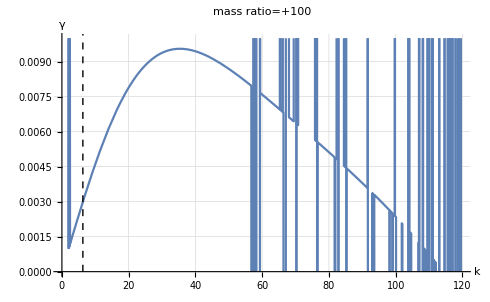

```mathematica
linestyle = {Dashed};
line = Line[{{6.28,0.0},{6.28,0.03}}];
Plot[p[k],{k,2,120},AxesOrigin->{0,0},GridLines->Automatic, AxesLabel->{k,γ}, Epilog->{Directive[linestyle],line}, PlotRange->{0.000,0.01}, PlotLabel->"mass ratio=" +1/ϵM,BaseStyle->{FontSize-> 20}]
```

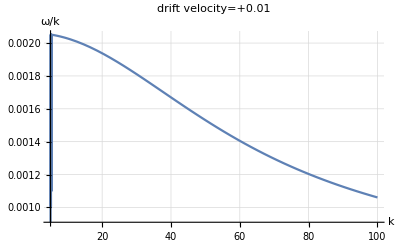

```mathematica
Plot[w[k]/k,{k,5,100},GridLines->Automatic,AxesLabel->{k,ω/k},PlotLabel->"drift velocity=" +u,BaseStyle->{FontSize-> 20}]
```

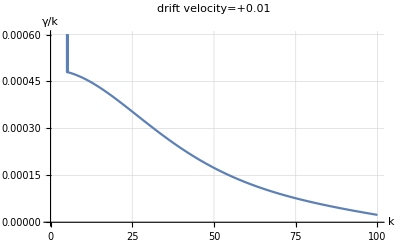

```mathematica
Plot[p[k]/k,{k,5,100},AxesOrigin->{0,0},GridLines->Automatic, AxesLabel->{k,γ/k},PlotLabel->"drift velocity=" +u,BaseStyle->{FontSize-> 20}, PlotRange->{0.0,0.0006}]
```

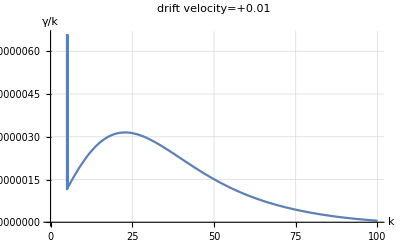

```mathematica
Plot[p[k]*p[k]/k,{k,5,100},AxesOrigin->{0,0},GridLines->Automatic, AxesLabel->{k,γ/k},PlotLabel->"drift velocity=" +u,BaseStyle->{FontSize-> 20}]
```